```mathematica
<<KerrGeodesics`
<<SpinWeightedSpheroidalHarmonics`
```

```mathematica
(*Params*)
l=3;
m=1;
k=2;
M=1;
a =.998M;
r0=10M;
θi = π/3;
xi = Cos[θi];

Δ[r_]:=r^2-2M r+a^2;
```

```mathematica
(*Frequencies wrt BL time*)
Freqs = KerrGeoFrequencies[a,r0,0,xi];
Ωθ = Freqs[[2]];
Ωϕ = Freqs[[3]];

ω = m Ωϕ+ k Ωθ;
```

```mathematica
(*Toolkit computes orbit parameterised by λ (Mino time), so we need to switch our integration variable*)
dtdλ[θ_]:=ℰ(((r0^2+a^2)^2)/Δ[r0]-a^2 Sin[θ]^2)+a ℒ(1-(r0^2+a^2)/Δ[r0]);
Υθ=KerrGeoFrequencies[a,r0,0,xi,Time->"Mino"][[2]];
Λθ = (2π)/Υθ;
```

```mathematica
Consts = KerrGeoConstantsOfMotion[a,r0,0,xi];
ℰ=Consts[[1]];
ℒ=Consts[[2]];
Q = Consts[[3]];
```

```mathematica
S[θ_]:=SpinWeightedSpheroidalHarmonicS[0,l,m,a ω, θ,0];
```

```mathematica
orbit=KerrGeoOrbit[a,r0,0,xi];
{tp,rp,θp,ϕp}=orbit["Trajectory"];
```

```mathematica
(*Calculating 4 velocity*)
gtt[M_,a_,r_,θ_]:=-((a^4+2 r^4+a^2 r (2 M+3 r)+a^2 (a^2+r (-2 M+r)) Cos[2 θ])/((a^2+r (-2 M+r)) (a^2+2 r^2+a^2 Cos[2 θ])))
gtϕ[M_,a_,r_,θ_]:=-(4 a M r)/((a^2+r (-2 M+r)) (a^2+2 r^2+a^2 Cos[2 θ]))
ut[M_,a_,r_,θ_,ℰ_,ℒ_]:=gtϕ[M,a,r,θ]ℒ-gtt[M,a,r,θ]ℰ
```

```mathematica
gtϕ[My,ay,r0y,θp[λ]]
```

-((4 ay My r0y)/((ay^2+r0y (-2 My+r0y)) (ay^2+2 r0y^2+ay^2 Cos[2 ArcCos[1/2 √3 JacobiSN[1.00132 (π/2+3.57818 λ),0.00527414]]])))

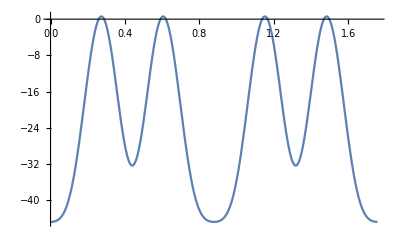

```mathematica
Integrand[λ_]:=S[θp[λ]]/ut[M,a,r0,θp[λ],ℰ,ℒ] Cos[(ω tp[λ]-m ϕp[λ])]dtdλ[θp[λ]];
Plot[Integrand[λ],{λ,0,Λθ}]
```

```mathematica
n=1000;
δλ = Λθ/n
```

0.00175597

```mathematica
NIntegrate[Integrand[λ],{λ,0,Λθ},Method->"Trapezoidal"]//Chop
```

-40.0328

```mathematica
0.07243866603935412
```

0.0724387

```mathematica
Sum[(Integrand[λ-δλ]+Integrand[λ])/2 δλ,{λ,δλ,Λθ,δλ}]//Chop
```

0

```mathematica
0.07243866603936883-1.2106255668081767*^-14 ⅈ
```

0.0724387-1.21063×10^-14 ⅈ

```mathematica
0.07243866603934468+7.105427357601002*^-15 ⅈ
```

0.0724387+7.10543×10^-15 ⅈ

```mathematica
δλ/2(Integrand[0]+Integrand[Λθ]+2Sum[Integrand[λ],{λ,δλ,Λθ-δλ,δλ}])
```

-1.71558×10^-14-1.53864×10^-14 ⅈ

```mathematica
0.07243866603934468+7.327471962526033*^-15 ⅈ
```

0.0724387+7.32747×10^-15 ⅈ

```mathematica
0.0724386660393439+5.8499747326301205*^-15 ⅈ
```

0.0724387+5.84997×10^-15 ⅈ